```mathematica
Clear["Global`*"]
```

```mathematica
(*Физические константы*)
```

```mathematica
c=3 10^8;(*м/с*)
h=6.63 10^-34;(*Планк*)
NN=6.62 10^22 ;(*1/м^3*)(*Перевод  концентрации из ppm в 1/м^3*)
```

```mathematica
(*Параметры среды*)
d=10.5 10^-6;(*m*) (*MFD*)
A=N[(π d^2)/4];(*m^2*) (*Mode Area*)
(*α =6 10^-3; *)(*absorption*)(*1/m*)(* ~22dB/km *) (*Smith1972 pp4*) (*!!!*)
α0dB=0.2/10^3;(*dB/m*)(*потери в пассивном волокне*)
α1dB=0.08;(*dB/m*)(*потери в активном волокне*)(*значение для YbEr 6000 ppm*)
α0=N[Log[10^(α0dB/10)]];(*1/м*)
α1=N[Log[10^(α1dB/10)]];(*1/м*)
τ=1.45 10^-3;(*с*)
Δν=13.; (*GHz*)(*сдвиг ВРМБ*)
gb =N[5. 10^-12]; (*m/W*)(*ВРМБ усиление*)
N0=5400.;
(*NN0[z_,L1_,L2_]:=N0(HeavisideTheta[z-L1])(1-HeavisideTheta[z-(L1+L2)]);(*ppm*)*)
NN0[z_,L1_,L2_]:=N0(Erf[30(z-L1)]+1)(-Erf[30(z-L2-L1)]+1)/4;
```

```mathematica
(*Длины волн и коэффициенты перевода плотности фотонов в мощность P=ρ*W *)
λs=1064.;(*нм*)
λp=1030.;(*нм*)
λSt=(c λs)/(c-Δν λs);(*нм*)
Ws=(A h c NN)/(λs 10^-9);
Wp=(A h c NN)/(λp 10^-9);
WSt=(A h c NN)/(λSt 10^-9);
```

```mathematica
(*Сечения поглощения и люминесценции*)
(σ=Import[NotebookDirectory[]<>"CrossSection.xls",{"DataLegacy"}][[1,5;;,{12,15,16}]])//TableForm;
σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
σs12=σa[λs]NN;
σs21=σe[λs]NN;
σp12=σa[λp]NN;
σp21=σe[λp]NN;
σSt12=σa[λSt]NN;
σSt21=σe[λSt]NN;
```

```mathematica
(*Начальные параметры усилителя*)
L1= 1.7; (*m*) (*Пассивное волокно на входе в усилитель*)
L2=3.5;(*m*)(*Активное волокно*)
(*L3=2.;*)(*m*)(*Пассивное волокно на выходе усилителя*)
L[L3_]=L1+L2+L3; (*m*) (*Длина всего оптического тракта*)
Ps0=0.180; (*Вт*) (*Сигнал на входе в усилитель*)
```

```mathematica
(*Функция, которая описывает серые потери в волокне*)
(*α[z_,L1_,L2_]:=(α1-α0)(Tanh[20(z-L1-L2)]+1)(-Tanh[15(z-L2)]+1)/4+α0;*)
α[z_,L1_,L2_]:=(α1-α0)(Erf[30(z-L1)]+1)(-Erf[30(z-L2-L1)]+1)/4+α0;
```

```mathematica
(*Скоростные уравнения с учетом ВРМБ*)
eqns1={
0==Pp[z]/Wp(σp12 N1[z]-σp21 N2[z])+Ps[z]/Ws(σs12 N1[z]-σs21 N2[z])+PSt[z]/WSt(σSt12 N1[z]-σSt21 N2[z])-N2[z]/τ,
Ps'[z]==Ps[z](σs21 N2[z]-σs12 N1[z])-α[z,L1,L2] Ps[z]-gb/A Ps[z]PSt[z],
Pp'[z]==Pp[z](σp21 N2[z]-σp12 N1[z])-α[z,L1,L2] Pp[z],
PSt'[z]==-gb/A PSt[z] Ps[z]+α[z,L1,L2] PSt[z]-PSt[z](σSt21 N2[z]-σSt12 N1[z]),
N1[z]+N2[z]==NN0[z,L1,L2]};
sol0=Solve[eqns1[[{1,5}]],{N1[z],N2[z]}][[1]];
eqns2=Simplify[eqns1[[{2,3,4}]]/.%];
sol[Ppump_,L3_]:=NDSolve[{eqns2,PSt[L[L3]]==bin Ps[L[L3]],Pp[0]==Ppump,Ps[0]==Ps0},{Pp,Ps,PSt},{z,0,L[L3]},AccuracyGoal->8][[1]];
```

```mathematica
(*Экспериментальные данные*)
(BR193cm=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;,{3,12}]])//TableForm;
BR193cm[[All,2]]=Abs[BR193cm[[All,2]]-BR193cm[[1,2]]]/1000.;
(BR256cm=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;26,{5,13}]])//TableForm;
BR256cm[[All,2]]=Abs[BR256cm[[All,2]]-BR256cm[[1,2]]]/1000.;
(BR302cm=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;25,{9,14}]])//TableForm;
BR302cm[[All,2]]=Abs[BR302cm[[All,2]]-BR302cm[[1,2]]]/1000.;
(WW193cm=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;,{15,3}]])//TableForm;
(WW256cm=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;26,{15,5}]])//TableForm;
(WW302cm=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;25,{15,9}]])//TableForm;
(P1030=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;,15]])//TableForm;
P1030[[1]]=0.5;
```

```mathematica
(*Сравнение Ватт-Ваттных характеристик*)
```

```mathematica
gb=5. 10^-11;(*m/W*)
bin=4. 10^-6;
L3=1.93;
```

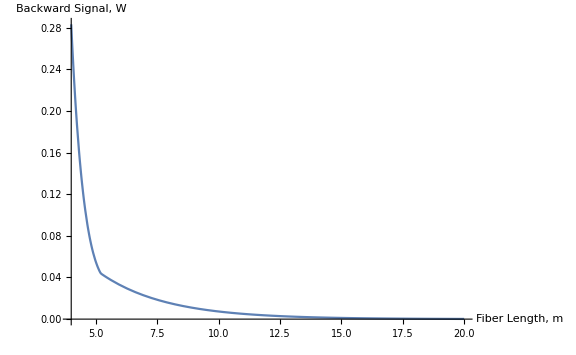

```mathematica
Plot[Evaluate[(PSt[z]/.sol[24.25,20.])],{z,4.,20.},PlotRange->All,AxesLabel->{"Fiber Length, m","Backward Signal, W"},ImageSize->Large,LabelStyle->Directive[Black,Bold,Medium]]
```

```mathematica
L1+L2
10 Log10[(PSt[L1+L2]/.sol[24.25,20.])/(PSt[L[20.]]/.sol[24.25,20.])]
```

5.2

32.3475

```mathematica
(*
В пассивном волокне сигнал усиливается, как и должно быть. 
Чем длиннее пассивное волокно, тем больше в нём усиливается сигнал, и тем больше будет "начальный" сигнал стокса на сходе в активное волокно. Это приведёт к большему усилению и, как следствие, ещё большему сигналу Стокса в z = 0. 
Основное усиление происходит в активном волокне, однако пассивное волокно влияет на величину этого усиления, увеличивая входной сигнал Стокса в активное волокно.
Сама величина сигнала, до которой возрос начальный сигнал, пройдя пассивное волокно, может быть небольшой, однако, из рассчета выше получается, что на двадцати метрах пассивного волокна усиление будет 32 дБ. 
*)
```

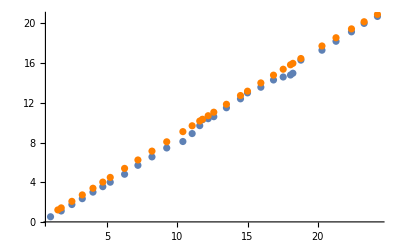

```mathematica
gb=N[5. 10^-11];(*m/W*)
bin=4. 10^-6;
WW193th=Transpose[{P1030,Table[Ps[L[1.93]]/.sol[Ppump,1.93],{Ppump,P1030}]}];
Show[ListPlot[WW193cm,PlotRange->All],ListPlot[WW193th,PlotRange->All,PlotStyle->Orange]]
```

```mathematica
f1=FindFit[WW193cm,a*x+b,{a,b},x]
f2=FindFit[WW193th,a*x+b,{a,b},x]
```

{a→0.875901,b→-0.51125}

{a→0.875339,b→-0.0476943}

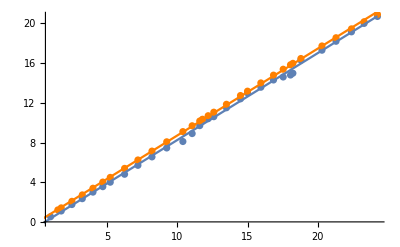

```mathematica
Show[ListPlot[WW193cm,PlotRange->All],ListPlot[WW193th,PlotRange->All,PlotStyle->Orange],
Plot[(a*x+b)/.f1,{x,0,24.25}],Plot[(a*x+b)/.f2,{x,0,24.25},PlotStyle->Orange]]
```

```mathematica
(*Поиск коэффициентов ВРМБ*)
Σ=List[];
Bin=List[];
gb=5. 10^-11;(*m/W*)
bin=4. 10^-6;
L3=1.93;
bstep=1. 10.^-6;
Monitor[For[i=0,i<4,i++,
BackSignalTable=ParallelTable[{(Ps[L[L3]]/.sol[Ppump,L3]),(PSt[0]/.sol[Ppump,L3])},{Ppump,P1030}];
BackSignalInt[x_]=Interpolation[BackSignalTable,InterpolationOrder->1][x];
BackSignalTable=Transpose[{BR193cm[[All,1]],ParallelTable[BackSignalInt[Psp],{Psp,BR193cm[[All,1]]}]}];
(*Σ=Insert[Σ,Total[(BackSignalTable[[-10;;,2]]-BR193cm[[-10;;,2]])^2],-1];*)
Σ=Insert[Σ,Max[Abs[(BackSignalTable[[-5;;,2]]-BR193cm[[-5;;,2]])]],-1];(* другой критерий *)
Bin=Insert[Bin,bin,-1];
Print[bin];
Print[Σ[[-1]]];
bin+=bstep;
],
Show[ListPlot[BR193cm,PlotRange->All],ListPlot[BackSignalTable,Joined->True,PlotRange->All]]
]
```

```mathematica
For[i=0,i≤ 6,i+=1,
binPos=Position[Σ,Min[Σ]][[1,1]];
Monitor[For[bin=Bin[[binPos]]-bstep/2,bin≤ Bin[[binPos]]+bstep/2,bin+=bstep,
BackSignalTable=ParallelTable[{(Ps[L[L3]]/.sol[Ppump,L3]),(PSt[0]/.sol[Ppump,L3])},{Ppump,P1030}];
BackSignalInt[x_]=Interpolation[BackSignalTable,InterpolationOrder->1][x];
BackSignalTable=Transpose[{BR193cm[[All,1]],ParallelTable[BackSignalInt[Psp],{Psp,BR193cm[[All,1]]}]}];
(*Σ=Insert[Σ,Total[(BackSignalTable[[-10;;,2]]-BR193cm[[-10;;,2]])^2],-1];*)
Σ=Insert[Σ,Max[Abs[(BackSignalTable[[-5;;,2]]-BR193cm[[-5;;,2]])]],-1];
Bin=Insert[Bin,bin,-1];
],
Show[ListPlot[BR193cm,PlotRange->All],ListPlot[BackSignalTable,Joined->True,PlotRange->All]]
];
Print[i];
Print[Bin];
Print[Σ];
bstep=bstep/2;
]
```

InterpolatingFunction::dmval: Input value {0.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

0

{1.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,2.5×10^-6,3.5×10^-6}

{0.351959,0.234066,0.115488,0.122991,0.174851,0.0924405}

InterpolatingFunction::dmval: Input value {0.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

1

{1.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,2.5×10^-6,3.5×10^-6,3.25×10^-6,3.75×10^-6}

{0.351959,0.234066,0.115488,0.122991,0.174851,0.0924405,0.0857558,0.107714}

InterpolatingFunction::dmval: Input value {0.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

2

{1.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,2.5×10^-6,3.5×10^-6,3.25×10^-6,3.75×10^-6,3.125×10^-6,3.375×10^-6}

{0.351959,0.234066,0.115488,0.122991,0.174851,0.0924405,0.0857558,0.107714,0.100625,0.0848062}

InterpolatingFunction::dmval: Input value {0.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

3

{1.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,2.5×10^-6,3.5×10^-6,3.25×10^-6,3.75×10^-6,3.125×10^-6,3.375×10^-6,3.3125×10^-6,3.4375×10^-6}

{0.351959,0.234066,0.115488,0.122991,0.174851,0.0924405,0.0857558,0.107714,0.100625,0.0848062,0.0809894,0.0886236}

InterpolatingFunction::dmval: Input value {0.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

4

{1.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,2.5×10^-6,3.5×10^-6,3.25×10^-6,3.75×10^-6,3.125×10^-6,3.375×10^-6,3.3125×10^-6,3.4375×10^-6,3.28125×10^-6,3.34375×10^-6}

{0.351959,0.234066,0.115488,0.122991,0.174851,0.0924405,0.0857558,0.107714,0.100625,0.0848062,0.0809894,0.0886236,0.082037,0.0828974}

InterpolatingFunction::dmval: Input value {0.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

5

{1.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,2.5×10^-6,3.5×10^-6,3.25×10^-6,3.75×10^-6,3.125×10^-6,3.375×10^-6,3.3125×10^-6,3.4375×10^-6,3.28125×10^-6,3.34375×10^-6,3.29688×10^-6,3.32813×10^-6}

{0.351959,0.234066,0.115488,0.122991,0.174851,0.0924405,0.0857558,0.107714,0.100625,0.0848062,0.0809894,0.0886236,0.082037,0.0828974,0.0801769,0.0819449}

InterpolatingFunction::dmval: Input value {0.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

6

{1.×10^-6,2.×10^-6,3.×10^-6,4.×10^-6,2.5×10^-6,3.5×10^-6,3.25×10^-6,3.75×10^-6,3.125×10^-6,3.375×10^-6,3.3125×10^-6,3.4375×10^-6,3.28125×10^-6,3.34375×10^-6,3.29688×10^-6,3.32813×10^-6,3.28906×10^-6,3.30469×10^-6}

{0.351959,0.234066,0.115488,0.122991,0.174851,0.0924405,0.0857558,0.107714,0.100625,0.0848062,0.0809894,0.0886236,0.082037,0.0828974,0.0801769,0.0819449,0.0811081,0.0805124}

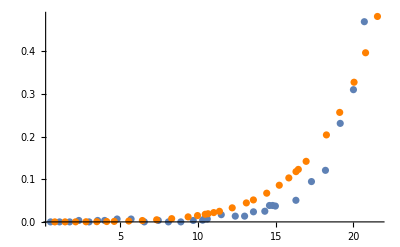

```mathematica
binPos=Position[Σ,Min[Σ]][[1,1]];
bin=Bin[[binPos]];
BackSignalTable=ParallelTable[{(Ps[L[L3]]/.sol[Ppump,L3]),(PSt[0]/.sol[Ppump,L3])},{Ppump,P1030}];
Show[ListPlot[BR193cm,PlotRange->All],ListPlot[BackSignalTable,Joined->True,PlotStyle->Orange,PlotRange->All],PlotRange->All]
```